```mathematica
Assume a functional
```

```mathematica
Integrate[1/(k Sqrt[2 π σ^2])Exp[(-(k-μ)^2)/(2 σ^2)]Log[(k^(5/2)ⅇ^(5/2)Sqrt[2 π σ^2])/(ρ Λ1^3 Exp[(-(k-μ)^2)/(2 σ^2)])],{k,1,Infinity}]
```

∫_1^∞ (ⅇ^(-(k-μ)^2/(2 σ^2)) Log[(ⅇ^(5/2+(k-μ)^2/(2 σ^2)) k^(5/2) √(2 π) √(σ^2))/(Λ1^3 ρ)])/(k √(2 π) √(σ^2))ⅆk

```mathematica
Integrate[1/k Exp[(-(k-μ)^2)/(2 σ^2)],{k,1,Infinity}]
```

NIntegrate::inumr: The integrand (ⅇ^(-(k-μ)^2/(2 σ^2)))/k has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.}}.

NIntegrate[Exp[-(k-μ)^2/(2 σ^2)]/k,{k,1,∞}]

```mathematica
Integrate[1/k,k]
```

Log[k]

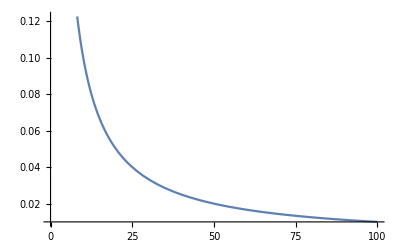

```mathematica
Plot[1/k,{k,0,100}]
```

```mathematica
Log[1]
```

0

```mathematica
Integrate[1/k,{k,1,Infinity}]
```

Integrate::idiv: Integral of 1/k does not converge on {1,∞}.

∫_1^∞ 1/k ⅆk

```mathematica
Integrate[k Exp[(-(k-μ)^2)/(2 σ^2)],{k,1,Infinity}]
```

ConditionalExpression[(√(π/2) μ)/(√(1/σ^2))+ⅇ^(-(-1+μ)^2/(2 σ^2)) σ^2+√(π/2) μ σ Erf[(-1+μ)/(√2 σ)],(Re[μ/σ^2]<0&&Re[σ^2]≥0)||Re[σ^2]>0]

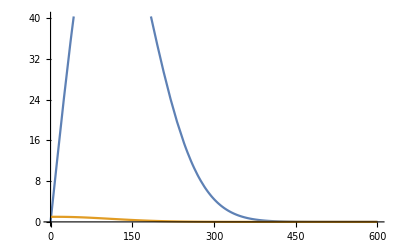

```mathematica
Plot[{k Exp[(-(k-10)^2)/(2 100^2)],Exp[(-(k-10)^2)/(2 100^2)]},{k,0,600}]
```

```mathematica
Clear[μ,σ]
```

```mathematica
Integrate[k^2 Exp[(-(k-μ)^2)/(2 σ^2)],{k,1,Infinity}]
```

ConditionalExpression[1/2 (2 ⅇ^(-(-1+μ)^2/(2 σ^2)) (1+μ) σ^2+(√(2 π) (μ^2+σ^2))/(√(1/σ^2))+(√(2 π) (μ^2+σ^2) Erf[(μ √(1/σ^2))/(√2)])/(√(1/σ^2))+(√(2 π) (-1+μ) (μ^2+σ^2) Erf[(√((-1+μ)^2/σ^2))/(√2)])/(√((-1+μ)^2/σ^2))-(√(2 π) μ (μ^2+σ^2) Erf[(√(μ^2/σ^2))/(√2)])/(√(μ^2/σ^2))),(Re[μ/σ^2]<0&&Re[σ^2]≥0)||Re[σ^2]>0]

```mathematica
Integrate[k^2 Exp[(-(k-μ)^2)/(2 σ^2)],{k,1,Infinity}]/(1/2 (2 ⅇ^(-(-1+μ)^2/(2 σ^2)) (1+μ) σ^2+(√(2 π) (μ^2+σ^2))/(√(1/σ^2))+(√(2 π) (μ^2+σ^2) Erf[(μ √(1/σ^2))/(√2)])/(√(1/σ^2))+(√(2 π) (-1+μ) (μ^2+σ^2) Erf[(√((-1+μ)^2/σ^2))/(√2)])/(√((-1+μ)^2/σ^2))-(√(2 π) μ (μ^2+σ^2) Erf[(√(μ^2/σ^2))/(√2)])/(√(μ^2/σ^2))))
```

ConditionalExpression[1,(Re[μ/σ^2]<0&&Re[σ^2]≥0)||Re[σ^2]>0]

10

100

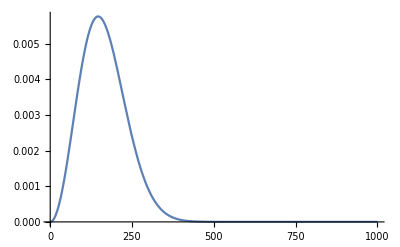

```mathematica
μ = 10
σ = 100
Plot[k^2 Exp[(-(k-μ)^2)/(2 σ^2)]/(1/2 (2 ⅇ^(-(-1+μ)^2/(2 σ^2)) (1+μ) σ^2+(√(2 π) (μ^2+σ^2))/(√(1/σ^2))+(√(2 π) (μ^2+σ^2) Erf[(μ √(1/σ^2))/(√2)])/(√(1/σ^2))+(√(2 π) (-1+μ) (μ^2+σ^2) Erf[(√((-1+μ)^2/σ^2))/(√2)])/(√((-1+μ)^2/σ^2))-(√(2 π) μ (μ^2+σ^2) Erf[(√(μ^2/σ^2))/(√2)])/(√(μ^2/σ^2)))),{k,1,1000}]
```

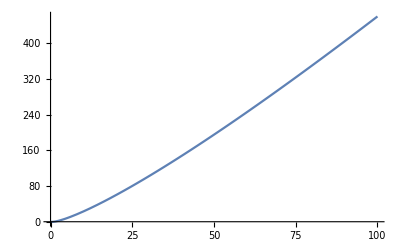

```mathematica
Plot[k Exp[(-(k-100)^2)/(2 1000^2)]Log[k],{k,0,100}]
```

```mathematica
Integrate[ k Exp[(-(k-μ)^2)/(2 σ^2)]Log[k],{k,0,Infinity}]
```

ConditionalExpression[1/4 (-2 ⅇ^(-μ^2/(2 σ^2)) EulerGamma σ^2-EulerGamma √(2 π) μ σ Erf[μ/(√2 σ)]+((√(2 π) μ)/(√(1/σ^2))+2 ⅇ^(-μ^2/(2 σ^2)) σ^2+√(2 π) μ σ Erf[μ/(√2 σ)]) Log[2]-(√(2 π) μ (-2+EulerGamma+Log[4]))/(√(1/σ^2))-(√(2 π) μ Log[1/σ^2])/(√(1/σ^2))-2 ⅇ^(-μ^2/(2 σ^2)) σ^2 Log[1/σ^2]-√(2 π) μ σ Erf[μ/(√2 σ)] Log[1/σ^2]-(√(2 π) μ Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/(2 σ^2)])/(√(1/σ^2))+2 ⅇ^(-μ^2/(2 σ^2)) σ^2 Hypergeometric1F1^(1,0,0)[1,1/2,μ^2/(2 σ^2)]),Re[σ^2]≥0]

```mathematica
NIntegrate[ k Exp[(-(k-10)^2)/(2 100^2)]Log[k],{k,0,1}]
```

-0.248861

```mathematica
N[-5/8 ExpIntegralEi[-1]]
```

0.137115

```mathematica
?ExpIntegralEi
```

ExpIntegralEi[z] gives the exponential integral function Ei(z).

```mathematica
f1 = Exp[(-(k-μ)^2)/(2 σ^2)]
```

ⅇ^(-1/200 (k-μ)^2)

```mathematica
Integrate[k*f1,{k,1,Infinity}]
```

100 ⅇ^(-1/200 (-1+μ)^2)+5 √(2 π) μ (1+Erf[(-1+μ)/(10 √2)])

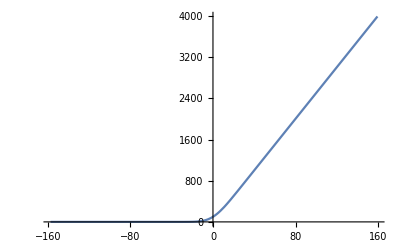

```mathematica
Plot[100 ⅇ^(-1/200 (-1+μ)^2)+5 √(2 π) μ (1+Erf[(-1+μ)/(10 √2)]),{μ,-157.33750602588105,159.33750602588105}]
```

```mathematica
Integrate[k^2 f1,{k,1,Infinity}]
```

100 ⅇ^(-1/200 (-1+μ)^2) (1+μ)+5 √(2 π) (100+μ^2) (1+Erf[(-1+μ)/(10 √2)])

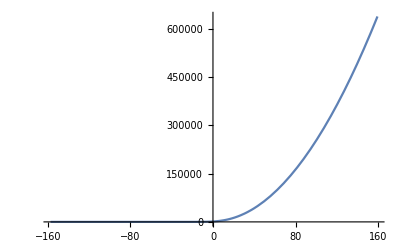

```mathematica
Plot[100 ⅇ^(-1/200 (-1+μ)^2) (1+μ)+5 √(2 π) (100+μ^2) (1+Erf[(-1+μ)/(10 √2)]),{μ,-157.33750602588105,159.33750602588105}]
```

```mathematica
Integrate[k(k-μ)^2 f1,{k,1,Infinity}]
```

-100 ⅇ^(-1/200 (-1+μ)^2) (-201+μ)+500 √(2 π) μ (1+Erf[(-1+μ)/(10 √2)])

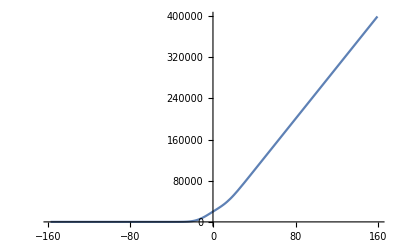

```mathematica
Plot[-100 ⅇ^(-1/200 (-1+μ)^2) (-201+μ)+500 √(2 π) μ (1+Erf[(-1+μ)/(10 √2)]),{μ,-157.33750602588105,159.33750602588105}]
```

```mathematica
Integrate[k f1 Log[(k^(5/2)ⅇ^(5/2))/(ρ Λ1^3)],{k,1,Infinity}]
```

∫_1^∞ ⅇ^(-1/200 (k-μ)^2) k Log[-2.08881×10^11 k^(5/2)]ⅆk

```mathematica
Integrate[k Exp[(-(k-μ)^2)/(2 σ^2)]Log[k],{k,0,Infinity}]
```

5/2 (-20 ⅇ^(-μ^2/200) EulerGamma+2 √(2 π) μ-EulerGamma √(2 π) μ-EulerGamma √(2 π) μ Erf[μ/(10 √2)]+60 ⅇ^(-μ^2/200) Log[2]+√(2 π) μ Log[2]+40 ⅇ^(-μ^2/200) Log[5]+√(2 π) μ Erf[μ/(10 √2)] Log[8]+√(2 π) μ Log[25]+√(2 π) μ Erf[μ/(10 √2)] Log[25]-√(2 π) μ Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/200]+20 ⅇ^(-μ^2/200) Hypergeometric1F1^(1,0,0)[1,1/2,μ^2/200])

```mathematica
N[%205]
```

748.321

```mathematica
N[-EulerGamma/4]
```

-0.144304

```mathematica
I4 = FullSimplify[1/(8 √(1/σ^2))(10 √(2 π) μ+(20 ⅇ^(-μ^2/(2 σ^2)))/(√(1/σ^2))-(10 ⅇ^(-μ^2/(2 σ^2)) EulerGamma)/(√(1/σ^2))+10 √(2 π) μ Erf[(μ √(1/σ^2))/(√2)]-5 EulerGamma √(2 π) μ √(1/σ^2) σ Erf[μ/(√2 σ)]+5 (√(2 π) μ+(2 ⅇ^(-μ^2/(2 σ^2)))/(√(1/σ^2))+√(2 π) μ √(1/σ^2) σ Erf[μ/(√2 σ)]) Log[2]-5 √(2 π) μ (-2+EulerGamma+Log[4])+4 √(2 π) μ Log[1/(Λ1^3 ρ)]+(8 ⅇ^(-μ^2/(2 σ^2)) Log[1/(Λ1^3 ρ)])/(√(1/σ^2))+4 √(2 π) μ Erf[(μ √(1/σ^2))/(√2)] Log[1/(Λ1^3 ρ)]-5 √(2 π) μ Log[1/σ^2]-(10 ⅇ^(-μ^2/(2 σ^2)) Log[1/σ^2])/(√(1/σ^2))-5 √(2 π) μ √(1/σ^2) σ Erf[μ/(√2 σ)] Log[1/σ^2]-5 √(2 π) μ Derivative[1,0,0][Hypergeometric1F1][0,3/2,-μ^2/(2 σ^2)]+(10 ⅇ^(-μ^2/(2 σ^2)) Derivative[1,0,0][Hypergeometric1F1][1,1/2,μ^2/(2 σ^2)])/(√(1/σ^2)))]
```

1/8 ⅇ^(-μ^2/(2 σ^2)) σ (20 σ-10 EulerGamma σ-5 ⅇ^(μ^2/(2 σ^2)) EulerGamma √(2 π) μ Erf[μ/(√2 σ)]+2 σ Log[32]+ⅇ^(μ^2/(2 σ^2)) √(2 π) μ Erf[μ/(√2 σ)] Log[32]+8 σ Log[1/(Λ1^3 ρ)]-10 σ Log[1/σ^2]-5 ⅇ^(μ^2/(2 σ^2)) √(2 π) μ Erf[μ/(√2 σ)] Log[1/σ^2]-ⅇ^(μ^2/(2 σ^2)) √(2 π) μ √(1/σ^2) σ (-30+5 EulerGamma+Log[32]-8 Log[1/(Λ1^3 ρ)]+2 Erfc[(μ √(1/σ^2))/(√2)] (5+2 Log[1/(Λ1^3 ρ)])+5 Log[1/σ^2]+5 Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/(2 σ^2)])+10 σ Hypergeometric1F1^(1,0,0)[1,1/2,μ^2/(2 σ^2)])

```mathematica
I5 = Integrate[k f1 Log[(k^(5/2)ⅇ^(5/2))/(ρ Λ1^3)],{k,0,1}]
```

∫_0^1 ⅇ^(-(k-μ)^2/(2 σ^2)) k Log[(ⅇ^(5/2) k^(5/2))/(Λ1^3 ρ)]ⅆk

```mathematica
Pk = -β((dg2 -2*dgn)*η*I1 + η*dgn*I2) - η/(2 σ^2)*I3 + η*I4 - η*I5
```

-1/4 η ((√(2 π) μ)/(√(1/σ^2))+ⅇ^(-(-1+μ)^2/(2 σ^2)) (2-2 μ+4 σ^2)+√(2 π) μ σ Erf[(-1+μ)/(√2 σ)])-β ((dg2-2 dgn) η ((√(π/2) μ)/(√(1/σ^2))+ⅇ^(-(-1+μ)^2/(2 σ^2)) σ^2+√(π/2) μ σ Erf[(-1+μ)/(√2 σ)])+dgn η (ⅇ^(-(-1+μ)^2/(2 σ^2)) (1+μ) σ^2+(√(π/2) (μ^2+σ^2))/(√(1/σ^2))+√(π/2) σ (μ^2+σ^2) Erf[(-1+μ)/(√2 σ)]))-η ∫_0^1 ⅇ^(-(k-μ)^2/(2 σ^2)) k Log[(ⅇ^(5/2) k^(5/2))/(Λ1^3 ρ)]ⅆk+1/8 ⅇ^(-μ^2/(2 σ^2)) η σ (20 σ-10 EulerGamma σ-5 ⅇ^(μ^2/(2 σ^2)) EulerGamma √(2 π) μ Erf[μ/(√2 σ)]+2 σ Log[32]+ⅇ^(μ^2/(2 σ^2)) √(2 π) μ Erf[μ/(√2 σ)] Log[32]+8 σ Log[1/(Λ1^3 ρ)]-10 σ Log[1/σ^2]-5 ⅇ^(μ^2/(2 σ^2)) √(2 π) μ Erf[μ/(√2 σ)] Log[1/σ^2]-ⅇ^(μ^2/(2 σ^2)) √(2 π) μ √(1/σ^2) σ (-30+5 EulerGamma+Log[32]-8 Log[1/(Λ1^3 ρ)]+2 Erfc[(μ √(1/σ^2))/(√2)] (5+2 Log[1/(Λ1^3 ρ)])+5 Log[1/σ^2]+5 Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/(2 σ^2)])+10 σ Hypergeometric1F1^(1,0,0)[1,1/2,μ^2/(2 σ^2)])

```mathematica
dPk = D[Pk,μ]
```

-1/4 η (-2 ⅇ^(-(-1+μ)^2/(2 σ^2))+2 ⅇ^(-(-1+μ)^2/(2 σ^2)) μ+(√(2 π))/(√(1/σ^2))-(ⅇ^(-(-1+μ)^2/(2 σ^2)) (-1+μ) (2-2 μ+4 σ^2))/σ^2+√(2 π) σ Erf[(-1+μ)/(√2 σ)])-β ((dg2-2 dgn) η (-ⅇ^(-(-1+μ)^2/(2 σ^2)) (-1+μ)+ⅇ^(-(-1+μ)^2/(2 σ^2)) μ+(√(π/2))/(√(1/σ^2))+√(π/2) σ Erf[(-1+μ)/(√2 σ)])+dgn η (-ⅇ^(-(-1+μ)^2/(2 σ^2)) (-1+μ) (1+μ)+(√(2 π) μ)/(√(1/σ^2))+ⅇ^(-(-1+μ)^2/(2 σ^2)) σ^2+ⅇ^(-(-1+μ)^2/(2 σ^2)) (μ^2+σ^2)+√(2 π) μ σ Erf[(-1+μ)/(√2 σ)]))-η ∫_0^1 (ⅇ^(-(k-μ)^2/(2 σ^2)) k (k-μ) Log[(ⅇ^(5/2) k^(5/2))/(Λ1^3 ρ)])/σ^2 ⅆk-1/(8 σ)ⅇ^(-μ^2/(2 σ^2)) η μ (20 σ-10 EulerGamma σ-5 ⅇ^(μ^2/(2 σ^2)) EulerGamma √(2 π) μ Erf[μ/(√2 σ)]+2 σ Log[32]+ⅇ^(μ^2/(2 σ^2)) √(2 π) μ Erf[μ/(√2 σ)] Log[32]+8 σ Log[1/(Λ1^3 ρ)]-10 σ Log[1/σ^2]-5 ⅇ^(μ^2/(2 σ^2)) √(2 π) μ Erf[μ/(√2 σ)] Log[1/σ^2]-ⅇ^(μ^2/(2 σ^2)) √(2 π) μ √(1/σ^2) σ (-30+5 EulerGamma+Log[32]-8 Log[1/(Λ1^3 ρ)]+2 Erfc[(μ √(1/σ^2))/(√2)] (5+2 Log[1/(Λ1^3 ρ)])+5 Log[1/σ^2]+5 Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/(2 σ^2)])+10 σ Hypergeometric1F1^(1,0,0)[1,1/2,μ^2/(2 σ^2)])+1/8 ⅇ^(-μ^2/(2 σ^2)) η σ (-(10 EulerGamma μ)/σ-5 ⅇ^(μ^2/(2 σ^2)) EulerGamma √(2 π) Erf[μ/(√2 σ)]-(5 ⅇ^(μ^2/(2 σ^2)) EulerGamma √(2 π) μ^2 Erf[μ/(√2 σ)])/σ^2+(2 μ Log[32])/σ+ⅇ^(μ^2/(2 σ^2)) √(2 π) Erf[μ/(√2 σ)] Log[32]+(ⅇ^(μ^2/(2 σ^2)) √(2 π) μ^2 Erf[μ/(√2 σ)] Log[32])/σ^2-(10 μ Log[1/σ^2])/σ-5 ⅇ^(μ^2/(2 σ^2)) √(2 π) Erf[μ/(√2 σ)] Log[1/σ^2]-(5 ⅇ^(μ^2/(2 σ^2)) √(2 π) μ^2 Erf[μ/(√2 σ)] Log[1/σ^2])/σ^2-ⅇ^(μ^2/(2 σ^2)) √(2 π) √(1/σ^2) σ (-30+5 EulerGamma+Log[32]-8 Log[1/(Λ1^3 ρ)]+2 Erfc[(μ √(1/σ^2))/(√2)] (5+2 Log[1/(Λ1^3 ρ)])+5 Log[1/σ^2]+5 Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/(2 σ^2)])-ⅇ^(μ^2/(2 σ^2)) √(2 π) μ^2 (1/σ^2)^(3/2) σ (-30+5 EulerGamma+Log[32]-8 Log[1/(Λ1^3 ρ)]+2 Erfc[(μ √(1/σ^2))/(√2)] (5+2 Log[1/(Λ1^3 ρ)])+5 Log[1/σ^2]+5 Hypergeometric1F1^(1,0,0)[0,3/2,-μ^2/(2 σ^2)])-ⅇ^(μ^2/(2 σ^2)) √(2 π) μ √(1/σ^2) σ (-2 ⅇ^(-μ^2/(2 σ^2)) √(2/π) √(1/σ^2) (5+2 Log[1/(Λ1^3 ρ)])-(5 μ Hypergeometric1F1^(1,0,1)[0,3/2,-μ^2/(2 σ^2)])/σ^2)+(10 μ Hypergeometric1F1^(1,0,1)[1,1/2,μ^2/(2 σ^2)])/σ)

```mathematica
Simplify[%94]
```

$Aborted

```mathematica
dg2 = -14.5;
dgn = -25;
h=6.626070040*10^-34;
kB=1.38064852*10^-23;
Da2kg=1.660539040*10^-27;
mmon=422.5;
ρ =9.04*10^25;
T = 298;
Λ1=h/Sqrt[2*π*mmon*Da2kg*kB*T];
σ = 100;
```

```mathematica
h
```

6.62607×10^-34

```mathematica
Λ1
```

4.92015×10^-12

```mathematica
h
```

-15.9885

```mathematica
β = 1/(kB T)
```

-0.000174349

```mathematica
-β((dg2 -2*dgn)*η*I1 + η*dgn*I2) - η/(2 σ^2)*I3 + η*I4
```

```mathematica
Clear[ePk]
```

```mathematica
ePk[μ_]:=  -β((dg2 -2*dgn)*η*I1 + η*dgn*I2) - η/(2 σ^2)*I3 + η*I4
```

```mathematica
ePk[100]
```

```mathematica
dePk = FullSimplify[D[ePk,μ]]
```

```mathematica
ePkm[μ_] := ePk
```

```mathematica
D[ePkm[μ],μ]
```

```mathematica
Clear[I1,I2,I3,I4,I5]
```

```mathematica
Clear[η,σ]
```

```mathematica
η[μ_,σ_]:= 1/Integrate[k Exp[(-(k-μ)^2)/(2 σ^2)],{k,0,Infinity},Assumptions->{σ>0,μ>0}]
```

```mathematica
η[μ,σ]
```

-(√(2/π))/(μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))

```mathematica
Plot3D[η[μ,σ],{μ,0,100},{σ,900,1000}]
```

-Graphics3D-

```mathematica
I1[μ_,σ_]:= Integrate[Exp[(-(k-μ)^2)/(2 σ^2)],{k,0,Infinity},Assumptions->{σ>0,μ>0}]
```

```mathematica
FullSimplify[I1[μ,σ]]
```

√(π/2) σ (1+Erf[μ/(√2 σ)])

```mathematica
I2[μ_,σ_]:= Integrate[k Exp[(-(k-μ)^2)/(2 σ^2)],{k,0,Infinity},Assumptions->{μ>0,σ>0}]
```

```mathematica
FullSimplify[I2[μ,σ]]
```

-√(π/2) μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])

```mathematica
I4[μ_,σ_]:=Integrate[ Exp[(-(k-μ)^2)/(2 σ^2)]Log[k],{k,0,Infinity},Assumptions->{μ>0,σ>0}]
```

```mathematica
FullSimplify[I4[μ,σ]]
```

1/4 (-√(2 π) σ (EulerGamma+Log[2]+Erf[μ/(√2 σ)] (EulerGamma-Log[2]-2 Log[σ])-2 Log[σ])-√(2 π) σ Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+2 ⅇ^(-μ^2/(2 σ^2)) μ Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)])

```mathematica
I3[μ_,σ_] := Integrate[(k-μ)^2 Exp[(-(k-μ)^2)/(2 σ^2)],{k,0,Infinity},Assumptions->{μ>0,σ>0}]
```

```mathematica
FullSimplify[I3[μ,σ]]
```

-ⅇ^(-μ^2/(2 σ^2)) μ σ^2+√(π/2) σ^3 (1+Erf[μ/(√2 σ)])

```mathematica
Clear[Pmax]
```

```mathematica
Pmax[μ_,σ_]:=η[μ,σ](-1(dg2-2dgn)+Log[ⅇ^(5/2)/(η[μ,σ]ρ Λ1^3)])I1[μ,σ]-1 η[μ,σ]dgn I2[μ,σ]+η[μ,σ]/2 I4[μ,σ]+η[μ,σ]/(2 σ^2)I3[μ,σ]
```

```mathematica
Pmax[10,800]
```

25.0035

```mathematica
NumberForm[25.003510587674256,16]
```

25.00351058767426

```mathematica
Pmax[5,760]
```

25.0035

```mathematica
NumberForm[25.003485469423325,16]
```

25.00348546942333

```mathematica
Pmax[3,760]
```

25.0035

```mathematica
NumberForm[25.003484750632513,16]
```

25.00348475063251

```mathematica
Pmax[1,760]
```

25.0035

```mathematica
D[Pmax[μ,σ],μ]
```

(ⅇ^(-μ^2/(2 σ^2)) (-ⅇ^(-μ^2/(2 σ^2)) μ σ^2+√(π/2) σ^3 (1+Erf[μ/(√2 σ)])))/(π (μ^2/σ^2)^(3/2) σ^5 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)+(7.05193×10^-10 (1+Erf[μ/(√2 σ)]) (-(1.13144×10^9 ⅇ^(-μ^2/(2 σ^2)) μ^2)/((μ^2/σ^2)^(3/2) σ)-1.41805×10^9 σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])))/(μ^2 σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)-(ⅇ^(-μ^2/(2 σ^2)) μ)/(√(2 π) σ^3 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+(-ⅇ^(-μ^2/(2 σ^2)) μ σ^2+√(π/2) σ^3 (1+Erf[μ/(√2 σ)]))/(√(2 π) μ^2 σ^3 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+(ⅇ^(-μ^2/(2 σ^2)) √(2/π) (1+Erf[μ/(√2 σ)]) (-35.5+Log[-1.41805×10^9 μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))/((μ^2/σ^2)^(3/2) σ^2 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)-(ⅇ^(-μ^2/(2 σ^2)) √(2/π) (-35.5+Log[-1.41805×10^9 μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))/(μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+((1+Erf[μ/(√2 σ)]) (-35.5+Log[-1.41805×10^9 μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))/(μ^2 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+(ⅇ^(-μ^2/(2 σ^2)) (-√(2 π) σ (EulerGamma+Log[2]+Erf[μ/(√2 σ)] (EulerGamma-Log[2]-2 Log[σ])-2 Log[σ])-√(2 π) σ Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+2 ⅇ^(-μ^2/(2 σ^2)) μ Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)]))/(4 π (μ^2/σ^2)^(3/2) σ^3 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)+(-√(2 π) σ (EulerGamma+Log[2]+Erf[μ/(√2 σ)] (EulerGamma-Log[2]-2 Log[σ])-2 Log[σ])-√(2 π) σ Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+2 ⅇ^(-μ^2/(2 σ^2)) μ Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)])/(4 √(2 π) μ^2 σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))-(-2 ⅇ^(-μ^2/(2 σ^2)) (EulerGamma-Log[2]-2 Log[σ])+2 ⅇ^(-μ^2/(2 σ^2)) Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)]-(2 ⅇ^(-μ^2/(2 σ^2)) μ^2 Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)])/σ^2+(√(2 π) μ Hypergeometric1F1^(1,0,1)[0,1/2,-μ^2/(2 σ^2)])/σ+(2 ⅇ^(-μ^2/(2 σ^2)) μ^2 Hypergeometric1F1^(1,0,1)[1,3/2,μ^2/(2 σ^2)])/σ^2)/(4 √(2 π) μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))

```mathematica
FullSimplify[%516]
```

$Aborted

```mathematica
FullSimplify[D[Pmax[μ,σ],μ]]
```

(ⅇ^(-μ^2/σ^2) (72.6352 ⅇ^(μ^2/σ^2) μ^2 σ^3-0.31831 μ √(μ^2/σ^2) σ^4+ⅇ^(μ^2/(2 σ^2)) (0.797885 μ^5-55.8057 μ^3 σ^2-28.9772 √(μ^2/σ^2) σ^5)+ⅇ^(μ^2/(2 σ^2)) (-28.7007 √(μ^2/σ^2) σ^5 Erf[μ/(√2 σ)]+0.398942 √(μ^2/σ^2) σ^5 Log[σ]+0.398942 √(μ^2/σ^2) σ^5 Erf[μ/(√2 σ)] Log[σ]+0.797885 √(μ^2/σ^2) σ^5 Log[-1.41805×10^9 μ σ (-2.+GammaRegularized[-1/2,μ^2/(2 σ^2)])]+0.797885 √(μ^2/σ^2) σ^5 Erf[μ/(√2 σ)] Log[-1.41805×10^9 μ σ (-2.+GammaRegularized[-1/2,μ^2/(2 σ^2)])]+μ^3 (0.797885 σ^2 Log[σ]+GammaRegularized[-1/2,μ^2/(2 σ^2)] (-0.398942 μ^2+27.9028 σ^2-0.398942 σ^2 Log[σ])+σ^2 (1.59577-0.797885 GammaRegularized[-1/2,μ^2/(2 σ^2)]) Log[-1.41805×10^9 μ σ (-2.+GammaRegularized[-1/2,μ^2/(2 σ^2)])])+0.5 ⅇ^(μ^2/(2 σ^2)) μ^2 σ^3 (-2. Log[σ]+GammaRegularized[-1/2,μ^2/(2 σ^2)] (-72.6352+1. Log[σ])+Erf[μ/(√2 σ)] (143.884-2. Log[σ]+GammaRegularized[-1/2,μ^2/(2 σ^2)] (-71.942+1. Log[σ]))+(1.+1. Erf[μ/(√2 σ)]) (-4.+2. GammaRegularized[-1/2,μ^2/(2 σ^2)]) Log[-1.41805×10^9 μ σ (-2.+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))-0.199471 ⅇ^(μ^2/(2 σ^2)) √(μ^2/σ^2) σ^5 Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+0.159155 μ √(μ^2/σ^2) σ^4 Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)]+ⅇ^(μ^2/σ^2) μ^2 σ (0.5-0.25 GammaRegularized[-1/2,μ^2/(2 σ^2)]) (σ^2 Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+μ^2 Hypergeometric1F1^(1,0,1)[0,1/2,-μ^2/(2 σ^2)])+ⅇ^(μ^2/(2 σ^2)) μ^5 (-2.+1. GammaRegularized[-1/2,μ^2/(2 σ^2)]) (0.199471 Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)]-0.199471 Hypergeometric1F1^(1,0,1)[1,3/2,μ^2/(2 σ^2)])))/(μ^4 σ^3 (-2.+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)

```mathematica
Solve[D[Pmax[μ,σ],μ]==0,μ]
```

Solve[(ⅇ^(-μ^2/(2 σ^2)) (-ⅇ^(-μ^2/(2 σ^2)) μ σ^2+√(π/2) σ^3 (1+Erf[μ/(√2 σ)])))/(π (μ^2/σ^2)^(3/2) σ^5 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)+(7.05193×10^-10 (1+Erf[μ/(√2 σ)]) (-(1.13144×10^9 ⅇ^(-μ^2/(2 σ^2)) μ^2)/((μ^2/σ^2)^(3/2) σ)-1.41805×10^9 σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])))/(μ^2 σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)-(ⅇ^(-μ^2/(2 σ^2)) μ)/(√(2 π) σ^3 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+(-ⅇ^(-μ^2/(2 σ^2)) μ σ^2+√(π/2) σ^3 (1+Erf[μ/(√2 σ)]))/(√(2 π) μ^2 σ^3 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+(ⅇ^(-μ^2/(2 σ^2)) √(2/π) (1+Erf[μ/(√2 σ)]) (-35.5+Log[-1.41805×10^9 μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))/((μ^2/σ^2)^(3/2) σ^2 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)-(ⅇ^(-μ^2/(2 σ^2)) √(2/π) (-35.5+Log[-1.41805×10^9 μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))/(μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+((1+Erf[μ/(√2 σ)]) (-35.5+Log[-1.41805×10^9 μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])]))/(μ^2 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))+(ⅇ^(-μ^2/(2 σ^2)) (-√(2 π) σ (EulerGamma+Log[2]+Erf[μ/(√2 σ)] (EulerGamma-Log[2]-2 Log[σ])-2 Log[σ])-√(2 π) σ Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+2 ⅇ^(-μ^2/(2 σ^2)) μ Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)]))/(4 π (μ^2/σ^2)^(3/2) σ^3 (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)])^2)+(-√(2 π) σ (EulerGamma+Log[2]+Erf[μ/(√2 σ)] (EulerGamma-Log[2]-2 Log[σ])-2 Log[σ])-√(2 π) σ Hypergeometric1F1^(1,0,0)[0,1/2,-μ^2/(2 σ^2)]+2 ⅇ^(-μ^2/(2 σ^2)) μ Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)])/(4 √(2 π) μ^2 σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))-(-2 ⅇ^(-μ^2/(2 σ^2)) (EulerGamma-Log[2]-2 Log[σ])+2 ⅇ^(-μ^2/(2 σ^2)) Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)]-(2 ⅇ^(-μ^2/(2 σ^2)) μ^2 Hypergeometric1F1^(1,0,0)[1,3/2,μ^2/(2 σ^2)])/σ^2+(√(2 π) μ Hypergeometric1F1^(1,0,1)[0,1/2,-μ^2/(2 σ^2)])/σ+(2 ⅇ^(-μ^2/(2 σ^2)) μ^2 Hypergeometric1F1^(1,0,1)[1,3/2,μ^2/(2 σ^2)])/σ^2)/(4 √(2 π) μ σ (-2+GammaRegularized[-1/2,μ^2/(2 σ^2)]))==0,μ]

```mathematica
Plot3D[Pmax[μ,σ],{μ,0,10},{σ,750,850}]
```

$Aborted

```mathematica
Maximize[{Pmax[μ,σ],μ>1,σ>0},{μ ,σ}]
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {Re[μ/σ^2]≤0,-Re[σ^2]≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

{25.0035,{μ→1.,σ→886.984}}

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
Pmax[500,600]
```

25.0035

```mathematica
Pmax[600,600]
```

25.0035

```mathematica
NumberForm[25.003464638494624,16]
```

25.00346463849462

```mathematica
Pmax[500,600]
```

25.0035

```mathematica
NumberForm[25.003491387235535,16]
```

25.00349138723553

```mathematica
Pmax[10000,10000]
```

25.0008

```mathematica
Pmax[6.127874010835699*10^-8,887.5223248278855]
```

25.0035+2.31791×10^-29 ⅈ

```mathematica
Abs[25.003530729797586+2.3179120234519657*^-29 ⅈ]
```

25.0035

```mathematica
NumberForm[25.003530729797586,16]
```

25.00353072979759